```mathematica
stack1 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

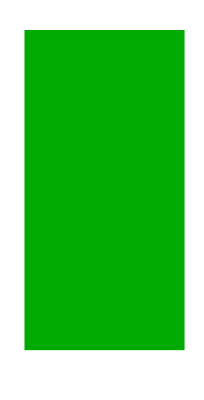

```mathematica
stack2 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

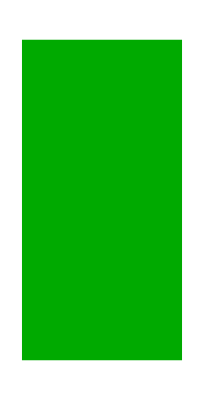

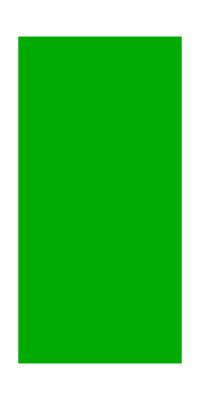

```mathematica
stack3 = Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]
```

```mathematica
DynamicModule[{pts={{0,0},{1,1},{2,0},{3,2}}},LocatorPane[Dynamic[pts],Dynamic[Plot[InterpolatingPolynomial[pts,x],{x,0,3},PlotRange->3]]]]
```

```mathematica
ListAnimate[Table[Graphics[Disk[],ImageSize->RandomReal[100]],{50}]]
```

```mathematica
ListAnimate[Table[Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}],{5}]]
```

```mathematica
FlipView[{stack1,stack2,stack3}]
```

```mathematica
list={Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}],Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}],Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}],Graphics[{Darker[Green],Rectangle[{3,0},{2,2}]}]};
ListAnimate[list,AnimationRunning->False]
```